# Analytical rate constants for 2-state ET model

## Marcus, Zusman, Rips-Jortner, Zusman^2, and Kramers-Grote-Hynes

## Constants

### Unit conversions

```mathematica
au2kcal=627.5095;
kcal2au=1/au2kcal;
ev2cm=8065.54477;
cm2ev = 1/ev2cm ;
au2ev=27.2113 ;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
au2ps=2.4189 10^-5;
fs2ps=10^-3;
ps2au=1/au2ps;
```

### Universal constants (atomic units)

```mathematica
hbar=1;
kb=3.16683 10^-6;
```

```mathematica
β[T_]:=1/(kb T au2kcal);
```

## Parameters governing nonadiabatic dynamics

Friction coefficient fo Onodera model (ps^-1) - characteristic time scale of relaxation (?):

```mathematica
γ[τO_,τD_]:=1/τO+1/τD;
```

Landau-Zener parameter:

```mathematica
αLZ[ϵ0_,ϵi_,τO_,τD_,V_,λ_,T_]:=Module[{f0,β,hb,τL},
f0=(4π ϵ0 ϵi)/(ϵ0-ϵi);
β=1/(kb T au2kcal);
hb=au2kcal au2ps;
τL=ϵi/ϵ0 τD;
(2π V^2)/hb √((τO τL β)/(2λ))
];
```

Characteristic frequency of nonadiabatic transitions (prefactor in Marcus expression):

```mathematica
Ωtr[V_,λ_,T_]:=Module[{β,hb},
β=1/(kb T au2kcal);
hb=au2kcal au2ps;
(2π V^2)/hb √((π β)/λ)
];
```

Characteristic time in the coupling region:

```mathematica
Ωcoup[ϵ0_,ϵi_,τO_,τD_,V_,λ_,T_]:=Module[{f0,β,τL},
f0=(4π ϵ0 ϵi)/(ϵ0-ϵi);
β=1/(kb T au2kcal);
τL=ϵi/ϵ0 τD;
1/V √(λ/(β τO τL))
];
```

Short time condition (must be much larger than 1 for Marcus expression):

```mathematica
ShortTimeCondition[T_,λ_,ϵ0_,ϵi_,τD_]:=(λ ϵi^2 τD^2)/(β[T] ϵ0^2 hbar^2 au2kcal^2 au2ps^2);
```

```mathematica
ShortTimeCondition[298,24.75,79,1.46,11]
```

2629.04

## Parameter estimates - are we in nonadiabatic regime?

Water (polarizable):

```mathematica
ϵ0=79.0;
ϵi=1.476;
τO=0.001818;
τD=11.5;
T=299;
λ=24.725;
V=0.05;
τL=ϵi/ϵ0 τD
```

0.214861

```mathematica
ShortTimeCondition[T,λ,ϵ0,ϵi,τD]
```

2943.68

```mathematica
αLZ[ϵ0,ϵi,τO,τD,V,λ,T]
```

0.00377325

```mathematica
γ[τO,τD]
```

550.142

Should be Ω_tr≪γ≪Ω_coup

```mathematica
{Ωtr[V,λ,T],γ[τO,τD],Ωcoup[ϵ0,ϵi,τO,τD,V,λ,T]}
```

{0.478553,550.142,3878.65}

## Marcus rate expression

V, λ, ΔG in kcal/mol, T in K, k in ps^-1

```mathematica
kMarcus[V_,λ_,ΔG_,T_]:=1/au2ps(2π)/hbar(V*kcal2au)^2 1/(√(4π λ kcal2au kb T))Exp[-β[T](λ+ΔG)^2/(4λ)];
```

```mathematica
kS=kMarcus[0.1,24.75,-19.75,298]
```

0.199124

## Zusman and Rips-Jortner rate expressions

V, λ, ΔG in kcal/mol; k in ps^-1

Rips-Jortner expression:

```mathematica
kRJ[V_,τL_,λ_,ΔG_,T_]:=1/au2ps(2π)/hbar(V*kcal2au)^2 1/(√(4π λ kcal2au kb T))1/(1+(4π)/hbar(V*kcal2au)^2((τL ps2au)/(λ kcal2au)))Exp[-β[T](λ+ΔG)^2/(4λ)];
```

```mathematica
kRJlimit[V_,τL_,λ_,ΔG_,T_]:=1/τL(√(λ kcal2au))/(√(16π kb T))Exp[-β[T](λ+ΔG)^2/(4λ)];
```

Rips-Jortner adiabaticity parameter:

```mathematica
ζRJ[V_,τL_,λ_]:=(4π)/(hbar au2kcal au2ps)(V^2 τL)/λ;
```

Zusman expression:

```mathematica
kZ[V_,τL_,λ_,ΔG_,T_]:=Module[{Ea,kstar,λfactor,k},
Ea=(λ+ΔG)^2/(4λ);
λfactor=1/(√(4π λ kb T au2kcal));
If[Ea==0,
k=((hbar au2kcal au2ps)/(2π V^2)1/λfactor+τL)^-1,
kstar=((hbar au2kcal au2ps)/(2π V^2)+τL(1/Abs[ΔG+λ]+1/Abs[ΔG-λ]))^-1;
k=kstar λfactor Exp[-Ea/(kb T au2kcal)]
];
k
];
```

```mathematica
kZlimit[V_,τL_,λ_,ΔG_,T_]:=1/τL(√(λ kcal2au))/(√(16π kb T))(1-ΔG^2/λ^2)Exp[-β[T](λ+ΔG)^2/(4λ)];
```

Zusman adiabaticity parameter:

```mathematica
ζZ[V_,τL_,λ_,ΔG_]:=(2π V^2)/(hbar au2kcal au2ps)τL(1/Abs[ΔG+λ]+1/Abs[ΔG-λ]);
```

Zusman expression for 2 relaxation periods:

```mathematica
kZ2[V_,δ1_,τL1_,δ2_,τL2_,λ_,ΔG_,T_]:=Module[{β,λ1,λ2,E1,E2,Ea,Ea2,ν1,ν2,k1,f2,k},
β=1/(kb T au2kcal);
λ1=λ δ1;
λ2=λ δ2;
Ea=(λ+ΔG)^2/(4λ);
Ea2=(λ2+ΔG)^2/(4λ2);
E1=ΔG+λ1;
E2=ΔG+λ2;
ν1=1/τL1;
ν2=1/τL2;
k1=1/au2ps(2π)/hbar(V*kcal2au)^2 1/(√(4π λ kcal2au kb T))Exp[-β(λ+ΔG)^2/(4λ)];
f2=(π^2 V^2)/(hbar au2kcal au2ps)(Exp[-β(Ea-Ea2)]/(ν2 √(λ λ2)Sin[(π E2)/(2λ2)])+1/(ν1 λ1 Sin[(π(ΔG+λ))/(2λ)]))+1;
k=k1 f2^-1;
k
];
```

Plots:

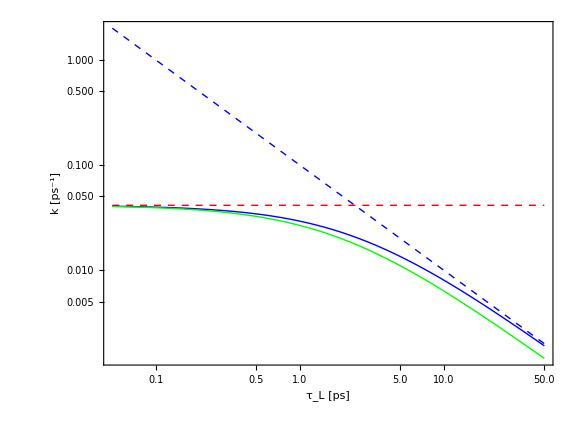

```mathematica
LogLogPlot[{kMarcus[0.1,20.0,-10,298],kRJ[0.1,x,20.0,-10,298],kRJlimit[0.1,x,20.0,-10,298],kZ[0.1,x,20.0,-10,298]},{x,0.05,50},PlotStyle->{{Red,Thick,Dashed},{Blue,Thick},{Blue,Thick,Dashed},{Green,Thick}},Axes->False,Frame->True,BaseStyle->{FontSize->24},FrameStyle->Thickness[0.0018],FrameLabel->{"τ_L [ps]","k [ps^-1]"},AspectRatio->0.75,ImageSize->Large]
```

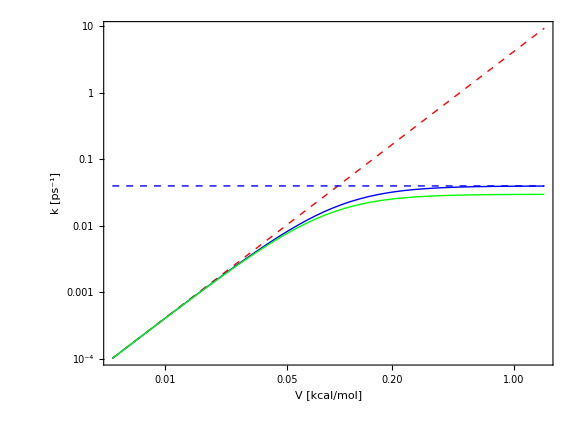

```mathematica
τ=2.5;
LogLogPlot[{kMarcus[V,20.0,-10,298],kRJ[V,τ,20.0,-10,298],kRJlimit[V,τ,20.0,-10,298],kZ[V,τ,20.0,-10,298]},{V,0.005,1.5},PlotStyle->{{Red,Thick,Dashed},{Blue,Thick},{Blue,Thick,Dashed},{Green,Thick}},Axes->False,Frame->True,BaseStyle->{FontSize->24},FrameStyle->Thickness[0.0018],FrameLabel->{"V [kcal/mol]","k [ps^-1]","τ_L = "<>ToString[τ]<>" ps"},AspectRatio->0.75,ImageSize->Large]
```

Including Zusman expression for two relaxation periods:

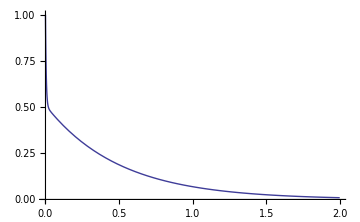

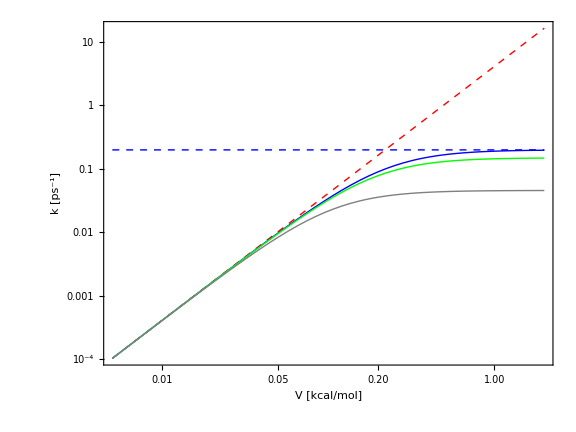

```mathematica
δ1=0.49;
τL1=0.005;
δ2=0.51;
τL2=0.5;
Plot[δ1 Exp[-t/τL1]+δ2 Exp[-t/τL2],{t,0,2},PlotRange->{0,1},ImageSize->Medium]
LogLogPlot[{kMarcus[V,20.0,-10,298],kRJ[V,τL2,20.0,-10,298],kRJlimit[V,τL2,20.0,-10,298],kZ[V,τL2,20.0,-10,298],kZ2[V,δ1,τL1,δ2,τL2,20.0,-10,298]},{V,0.005,2.0},PlotStyle->{{Red,Thick,Dashed},{Blue,Thick},{Blue,Thick,Dashed},{Green,Thick},{Gray,Thick}},Axes->False,Frame->True,BaseStyle->{FontSize->18},FrameStyle->Thickness[0.0018],FrameLabel->{"V [kcal/mol]","k [ps^-1]","δ_1 = "<>ToString[δ1]<>";   τ_L1 = "<>ToString[τL1]<>" ps;   "<>"δ_2 = "<>ToString[δ2]<>";   τ_L2 = "<>ToString[τL2]<>" ps"},AspectRatio->0.75,ImageSize->Large]
```

## KGH rate expression (for adiabatic reaction)

### Potential

Ground state adiabatic potential (for scaled energy gap coordinate):

```mathematica
Eg[x_,ϵ0_,ϵi_,V_,λ_,ΔG_]:=Module[{f0},
f0=(4π ϵ0 ϵi)/(ϵ0-ϵi);
1/2(f0 x^2-x √(2f0 λ)+λ+ΔG)-1/2 √((x √(2f0 λ)-λ-ΔG)^2+4 V^2)
];
```

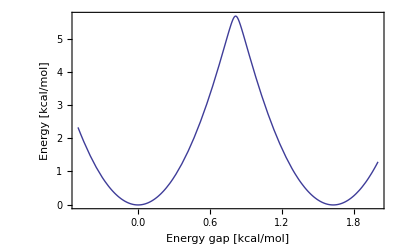

```mathematica
Plot[Eg[x,79,1.46,0.5,24.75,0],{x,-0.5,2.0},Axes->False,Frame->True,FrameLabel->{"Energy gap [kcal/mol]","Energy [kcal/mol]"}]
```

First derivative and barrier location:

```mathematica
DEg[x_,ϵ0_,ϵi_,V_,λ_,ΔG_]:=Module[{f0},
f0=(4π ϵ0 ϵi)/(ϵ0-ϵi);
1/2(2 f0 x-√(2f0 λ))-1/2(√(2f0 λ)(x √(2f0 λ)-λ-ΔG))/(√((x √(2f0 λ)-λ-ΔG)^2+4 V^2))
];
```

```mathematica
D2Eg[x_,ϵ0_,ϵi_,V_,λ_,ΔG_]:=Module[{f0},
f0=(4π ϵ0 ϵi)/(ϵ0-ϵi);
f0 (1-(4 V^2 λ)/((4 V^2+2f0 λ x^2+(ΔG+λ)(ΔG+λ-2x √(2f0 λ)))^(3/2)))
];
```

Reactant minimum:

```mathematica
rminimum[ϵ0_,ϵi_,V_,λ_,ΔG_]:=Module[{f0,rootlist,root1,root2,root3,kroot1,kroot2,kroot3,xm,Em},
Off[Solve::ratnz];
f0=(4π ϵ0 ϵi)/(ϵ0-ϵi);
rootlist=Solve[1/2(2 f0 x-√(2f0 λ))-1/2(√(2f0 λ)(x √(2f0 λ)-λ-ΔG))/(√((x √(2f0 λ)-λ-ΔG)^2+4 V^2))==0,x];
root1=rootlist⟦1,1,2⟧;
root2=rootlist⟦2,1,2⟧;
root3=rootlist⟦3,1,2⟧;
kroot1=f0 (1-(4 V^2 λ)/((4 V^2+2f0 λ root1^2+(ΔG+λ)(ΔG+λ-2root1 √(2f0 λ)))^(3/2)));
kroot2=f0 (1-(4 V^2 λ)/((4 V^2+2f0 λ root2^2+(ΔG+λ)(ΔG+λ-2root2 √(2f0 λ)))^(3/2)));
kroot3=f0 (1-(4 V^2 λ)/((4 V^2+2f0 λ root3^2+(ΔG+λ)(ΔG+λ-2root3 √(2f0 λ)))^(3/2)));
If[
Im[kroot1]==0&&kroot1>0,
xm=root1;
Em=1/2(f0 xm^2-xm √(2f0 λ)+λ+ΔG)-1/2 √((xm √(2f0 λ)-λ-ΔG)^2+4 V^2),
Print["No barrier! Abort..."];
Abort[]
];
{xm,Em,kroot1}
];
```

Force constant at the barrier top (unitless due to special scaling):

```mathematica
barrier[ϵ0_,ϵi_,V_,λ_,ΔG_]:=Module[{f0,rootlist,root1,root2,root3,kroot1,kroot2,kroot3,xb,Eb},
Off[Solve::ratnz];
f0=(4π ϵ0 ϵi)/(ϵ0-ϵi);
rootlist=Solve[1/2(2 f0 x-√(2f0 λ))-1/2(√(2f0 λ)(x √(2f0 λ)-λ-ΔG))/(√((x √(2f0 λ)-λ-ΔG)^2+4 V^2))==0,x];
root1=rootlist⟦1,1,2⟧;
root2=rootlist⟦2,1,2⟧;
root3=rootlist⟦3,1,2⟧;
kroot1=f0 (1-(4 V^2 λ)/((4 V^2+2f0 λ root1^2+(ΔG+λ)(ΔG+λ-2root1 √(2f0 λ)))^(3/2)));
kroot2=f0 (1-(4 V^2 λ)/((4 V^2+2f0 λ root2^2+(ΔG+λ)(ΔG+λ-2root2 √(2f0 λ)))^(3/2)));
kroot3=f0 (1-(4 V^2 λ)/((4 V^2+2f0 λ root3^2+(ΔG+λ)(ΔG+λ-2root3 √(2f0 λ)))^(3/2)));
If[
Im[kroot2]==0&&kroot2<0,
xb=root2;
Eb=1/2(f0 xb^2-xb √(2f0 λ)+λ+ΔG)-1/2 √((xb √(2f0 λ)-λ-ΔG)^2+4 V^2),
Print["No barrier! Abort..."];
Abort[]
];
{xb,Eb,-kroot2}
];
```

```mathematica
barrier[79,1.46,0.6918,24.75,0]
```

{0.813656,5.4957,315.679}

### Characteristic equation (KGH)

```mathematica
Γ[t_]:=-γ Exp[-t/τα]+η DiracDelta[t];
```

```mathematica
LaplaceTransform[Γ[t],t,s,Assumptions->{γ>0,η>0,τα>0}]
```

η-γ/(s+1/τα)

```mathematica
ΓL[s__]:=η-γ/(s+1/τα);
```

KGH equation for prefactor:

```mathematica
Ω(Ω+1/μ ΓL[Ω])-ωb^2==0
```

Ω (Ω+(η-γ/(1/τα+Ω))/μ)-ωb^2==0

or (after multiplying with μ:

```mathematica
μ Ω^2+Ω( η-γ/(Ω+1/τα))-μ ωb^2==0
```

μ Ω^2+Ω (η-γ/(1/τα+Ω))-μ ωb^2==0

### Rate expression (Onodera^2 model)

KGH rate expression (in ps^-1)

```mathematica
kKGH[V_,λ_,ΔG_,ϵ0_,ϵinf_,μ_,γ_,η_,τα_,T_,OptionsPattern[{Verbosity->False}]]:=Module[{min,top,Emin,Etop,Eb,kmin,ktop,ω0,ωb,Ωlist,Ω,rate,rateTST,κ},
min=rminimum[ϵ0,ϵinf,V,λ,ΔG];
top=barrier[ϵ0,ϵinf,V,λ,ΔG];
Emin=min⟦2⟧;
Etop=top⟦2⟧;
Eb=Etop-Emin;
kmin=min⟦3⟧;
ktop=top⟦3⟧;
ω0=√(kmin/μ);
ωb=√(ktop/μ);
Ωlist=Solve[μ Ω^2+η Ω-(Ω γ)/(Ω+1/τα)-ktop==0,Ω];
If[OptionValue[Verbosity],
Print["Solutions of characteristic equation (ps^-1): ",Ωlist⟦{1,2,3},1,2⟧];
Print["Solutions of characteristic equation (cm^-1): ",Ωlist⟦{1,2,3},1,2⟧au2cm/ps2au];
Print["Barrier frequency (ps^-1,cm^-1): ",ωb," (",ωb au2cm/ps2au,")"];
Print["Reactant frequency (ps^-1,cm^-1): ",ω0," (",ω0 au2cm/ps2au,")"];
Print["Barrier height (kcal/mol): ",Eb]
];


Ω=Ωlist⟦3,1,2⟧;
rateTST=ω0/(2π)Exp[-β[T]Eb];
κ=Ω/ωb;
rate=κ rateTST;
If[OptionValue[Verbosity],
Print["TST rate constant (ps^-1): ",rateTST];
Print["Transmission coefficient: ",κ];
Print["Grote-Hynes rate constant (ps^-1): ",rate]
];
rate
];
```

Christine’s parameters o2c for λ=9.82 kcal/mol

```mathematica
ϵ0=97.913579;
ϵinf=1.0;
λ=9.82;
μ=0.00099;
γ=7.7944082;
η=0.1169727;
τα=0.103315;
```

```mathematica
Vel=0.6918;
ΔG=0;
kKGH[Vel,λ,ΔG,ϵ0,ϵinf,μ,γ,η,τα,298,Verbosity->True]
```

Solutions of characteristic equation (ps^-1): {-539.08,-9.34459,420.591}

Solutions of characteristic equation (cm^-1): {-2861.9,-49.6091,2232.86}

Barrier frequency (ps^-1,cm^-1): 467.862 (2483.81)

Reactant frequency (ps^-1,cm^-1): 113.071 (600.276)

Barrier height (kcal/mol): 5.57734

TST rate constant (ps^-1): 0.00146189

Transmission coefficient: 0.898963

Grote-Hynes rate constant (ps^-1): 0.00131419

0.00131419

```mathematica
kMarcus[0.1,λ,ΔG,298]
```

0.00766704

```mathematica
kKGH[1.5,λ,dG,ϵ0,ϵinf,μ,γ,η,τα,298,Verbosity->True]
```

Solutions of characteristic equation (ps^-1): {-384.056,-8.93852,265.162}

Solutions of characteristic equation (cm^-1): {-2038.9,-47.4533,1407.7}

Barrier frequency (ps^-1,cm^-1): 306.667 (1628.05)

Reactant frequency (ps^-1,cm^-1): 112.426 (596.853)

Barrier height (kcal/mol): 4.84

TST rate constant (ps^-1): 0.00504867

Transmission coefficient: 0.864656

Grote-Hynes rate constant (ps^-1): 0.00436537

0.00436537

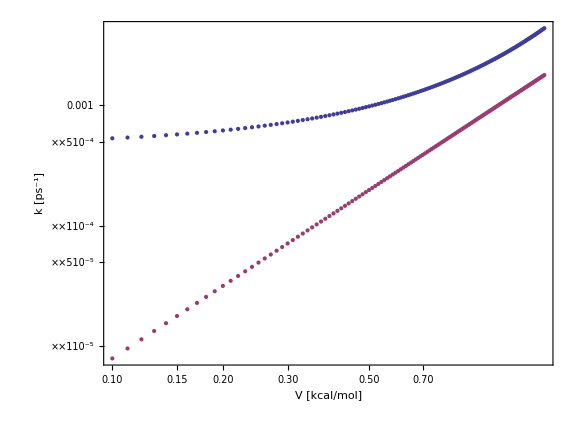

```mathematica
λ=25;
dG=0;
ListLogLogPlot[{Table[{V,kKGH[V,λ,dG,ϵ0,ϵinf,μ,γ,η,τα,298]},{V,0.1,1.5,0.01}],Table[{V,kMarcus[V,λ,dG,298]},{V,0.1,1.5,0.01}]},PlotRange->All,Axes->False,Frame->True,BaseStyle->{FontSize->18},FrameStyle->Thickness[0.0018],FrameLabel->{"V [kcal/mol]","k [ps^-1]"},AspectRatio->0.75,ImageSize->Large]
```

```mathematica
λ=25;
dG=0;
LogLogPlot[{kKGH[V,λ,dG,ϵ0,ϵinf,μ,γ,η,τα,298],kMarcus[V,λ,dG,298]},{V,0.1,1.5},Axes->False,Frame->True,BaseStyle->{FontSize->18},FrameStyle->Thickness[0.0015],FrameLabel->{"V [kcal/mol]","k [ps^-1]"},AspectRatio->0.75,ImageSize->Large,PlotPoints->2,MaxRecursion->0]
```

$Aborted

## Marcus parabola

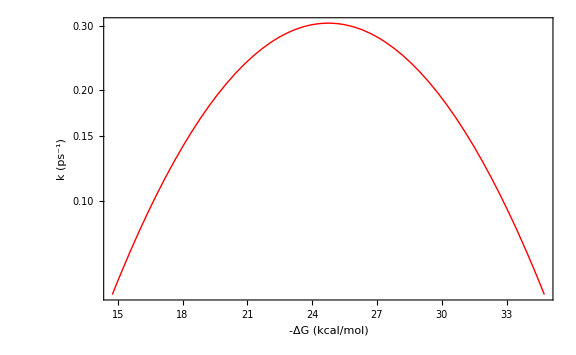

```mathematica
Er=24.75;
LogPlot[kMarcus[0.1,Er,-g,298],{g,Er-10,Er+10},PlotStyle->{Red},ImageSize->Large,PlotRange->All,
BaseStyle->{FontSize->20,FontFamily->"Helvetica"},
Axes->False,
Frame->True,
FrameLabel->{"-ΔG (kcal/mol)","k (ps^-1)"}]
```

## Set directory with data files

```mathematica
SetDirectory[NotebookDirectory[]]
```

/gpfs/home/avs10/Projects/mathematica

```mathematica
NotebookDirectory[]
```

/gpfs/home/avs10/Projects/mathematica/

```mathematica
Directory[]
```

/gpfs/home/avs10/Projects/mathematica

## Solution of kinetic equations

```mathematica
P1[dG_,T_,k_,t_]:=Module[{A,B,Δ},
Δ=β[T] dG;
A=k(1+Exp[Δ]);
B=Exp[-Δ];
(1+B Exp[-A t])/(1+B)
];
```

```mathematica
P2[dG_,T_,k_,t_]:=Module[{A,B,Δ},
Δ=β[T] dG;
A=k(1+Exp[Δ]);
B=Exp[-Δ];
(B(1-Exp[-A t]))/(1+B)
];
```

Population dynamics with Marcus rate constant for Christine’s parameters:

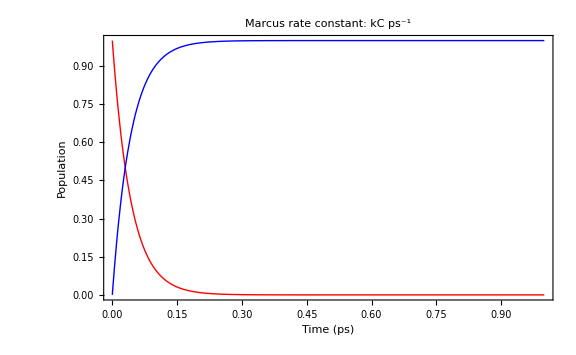

```mathematica
Plot[{P1[-9.82,298,kS,t],P2[-9.82,298,kS,t]},{t,0,1},PlotStyle->{Red,Blue},ImageSize->Large,PlotRange->All,
BaseStyle->{FontSize->20,FontFamily->"Helvetica"},
Axes->False,
Frame->True,
FrameLabel->{"Time (ps)","Population"},
PlotLabel->"Marcus rate constant: "<>ToString[ScientificForm[kC,4],FormatType->StandardForm]<>" ps^-1"]
```

## Fit of simulated diabatic populations

We are trying to fit the following data:

```mathematica
data=Import["dia_pop.dat"];
```

```mathematica
npoints=Length[data]
```

25001

```mathematica
P1data=data⟦Range[500],{1,2}⟧;
```

```mathematica
P2data=data⟦Range[500],{1,3}⟧;
```

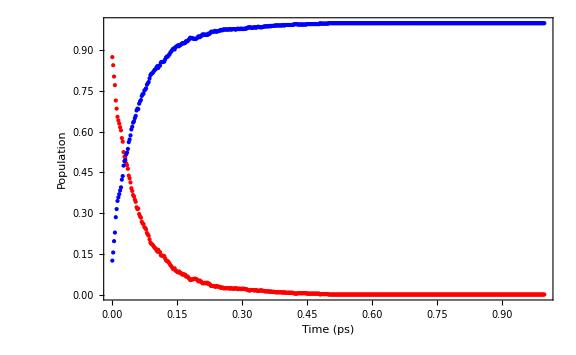

```mathematica
ListPlot[{P1data,P2data},Axes->False,Frame->True,PlotRange->All,FrameLabel->{"Time (ps)","Population"},PlotStyle->{Red,Blue},ImageSize->Large]
```

Rate constant fitting function
Arguments:
k0 - Guess for the rate constant value (shouldn’t be close, but the closer the better), in ps^-1;
dG - reaction free energy (in kcal/mol);
T - temperature in K;
datafile - name of the file with population data (it is assumed that the first column is time given in ps).

```mathematica
rateconstant[k0_,dG_,T_,datafile_,nPoints_]:=Module[{rawdata,time,dataP1,P1,fit,B,A,A0,t},
A0=k0(1+Exp[β[T]dG]);
rawdata=ReadList[datafile,{Real,Real,Real}];
dataP1=rawdata⟦Range[nPoints],{1,2}⟧;
P1=dataP1;
B=Exp[-β[T] dG];
fit=FindFit[P1,(1+B Exp[-A t])/(1+B),{{A,A0}},t];
fit⟦1,2⟧/(1+Exp[β[T] dG])
];
```

## Fitting Games

```mathematica
kfit=rateconstant[20.0,-9.82,298,"dia_pop.dat",500]
```

19.4575

Quality of the fit:

```mathematica
kmy=kfit;
```

```mathematica
tmin=0;
tmax=P1data⟦-1,1⟧
```

0.998

Solid lines: Marcus populations

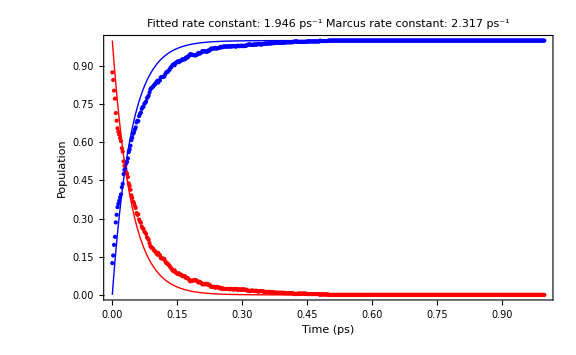

```mathematica
Show[
ListPlot[{P1data,P2data},PlotStyle->{{Red,PointSize->Tiny},{Blue,PointSize->Tiny}}],
Plot[{P1[-9.82,298,kS,t],P2[-9.82,298,kS,t]},{t,tmin,tmax},PlotStyle->{Red,Blue},PlotRange->All],
ImageSize->Large,PlotRange->All,
BaseStyle->{FontSize->20,FontFamily->"Helvetica"},
Axes->False,
Frame->True,
FrameLabel->{"Time (ps)","Population"},
PlotLabel->"Fitted rate constant: "<>ToString[ScientificForm[kmy,4],FormatType->StandardForm]<>" ps^-1"<>"\n"<>"Marcus rate constant: "<>ToString[ScientificForm[kS,4],FormatType->StandardForm]<>" ps^-1"
]
```